## Styles and custom color maps

```mathematica
width=2;
framewidth=1.5;
```

```mathematica
fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f)
OpaqueBox[legend_]:=Graphics[{{White,Opacity[0.5],Rectangle[]},Inset[legend,{0.5,0.6},Center]}]
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;
FrameLabelSize = 12;
PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},
LabelStyle->{Directive[Black,FontSize->FrameLabelSize,FontFamily->"Arial"]},
AspectRatio->0.75,ImageSize->400,(*PlotStyle->styles,*)PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[ListLogPlot,PlotOptions];
SetOptions[ListLogLinearPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
SetOptions[ParametricPlot,PlotOptions];
PlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],PlotPoints->60,MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"}};
SetOptions[Plot3D,PlotOptions3D];
ListPlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"},ColorFunction->"SunsetColors"};
SetOptions[ListPlot3D,ListPlotOptions3D];
DensityPlotOptions = {PlotPoints->60,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[DensityPlot,DensityPlotOptions];
ListDensityPlotOptions = {PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[ListDensityPlot,ListDensityPlotOptions];
```

```mathematica
Legending`LegendDump`$DefaultMarkerStyle=EdgeForm[Opacity[1]];
```

```mathematica
ColorHelix[z_] := Module[{start,rot,gamma,amp,angle,red,green,blue,min,max},
start=0.6;
rot=1.5;  
angle=2.0*Pi*(start/3.0+rot*z);
amp = 0.15;
red=z+amp(-0.14861 Cos[angle]+1.78277Sin[angle]);green=z+amp(-0.29227 Cos[angle]-0.90649Sin[angle]);blue=z+amp(1.97294*Cos[angle]);
RGBColor[Abs[Sqrt[1-red]],Abs[Sqrt[1-green]],Abs[Sqrt[1-blue]]]
]
```

## Definitions and Setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica

```mathematica
(*myWarmup = ParallelSum[i,{i,1,1000}]; *)(* launches the kernels necessary so that there are no issues below *)
```

## Data files

```mathematica
dataDir = "output_1kNpTraj";energy = "8.16";
(*dataDir = "run-aa8tev"; energy = "8.16";*)
(*dataDir = "run-aa2tev"; energy = "2.76";*)

(*dataDir = "run-aa1"; energy = "5.02";*)
(*dataDir = "run-aa2"; energy = "5.02";*)
(*dataDir = "run-aa3"; energy = "5.02";*)
```

```mathematica
labelMap = Association[
{"output_1kNpTraj"->"p+Pb; κ̂ = 6, γ̂ = 0, T_F = 170 MeV, τ_med = 0.6 fm; 8.16 TeV",
"run-aa8tev"->"p+Pb; κ̂ = 6, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm; 5.02 TeV; runs_20240110_5172"}]
```

<|output_1kNpTraj→p+Pb; κ̂ = 6, γ̂ = 0, T_F = 170 MeV, τ_med = 0.6 fm; 8.16 TeV,run-aa8tev→p+Pb; κ̂ = 6, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm; 5.02 TeV; runs_20240110_5172|>

```mathematica
keys=Keys[labelMap];
figureNameMap=Table[keys[[i]]->keys[[i]],{i,1,Length[keys]}]//Association;
```

```mathematica
datafile = "/input/"<>dataDir<>"/datafile.gz"
```

/input/output_1kNpTraj/datafile.gz

```mathematica
dirName = wd<>"/output-"<>energy<>"/"<>figureNameMap[dataDir];
If[!DirectoryQ[dirName ],CreateDirectory[dirName]];
```

## Load S and P wave data

```mathematica
rawDataAll=Partition[Import[wd<>datafile,"Table"],2];
Length[rawDataAll]
```

2000

```mathematica
selectL[lval_]:=Select[rawDataAll,#[[2,8]]==lval&]
```

```mathematica
rawDataS = selectL[0];
Length[rawDataS]
rawDataP = selectL[1];
Length[rawDataP]
```

1000

1000

```mathematica
myR = RandomInteger[{1,Length[rawDataS]}]
rawDataS[[myR ]]
rawDataP[[myR ]]
```

8

{{4.71035,0.395958,-1.13165,-1.69229,1.74292,2.99421,-1.69229},{0.814234,0.825668,0,0.673389,0,0,0,0}}

{{4.71035,0.395958,-1.13165,-1.69229,1.74292,2.99421,-1.69229},{0,0,1.19626,0,0.81058,0,0,1}}

```mathematica
sData=Transpose[{rawDataS[[All,2,1]], rawDataS[[All,2,2]], rawDataP[[All,2,3]], rawDataS[[All,2,4]], rawDataP[[All,2,5]], rawDataS[[All,2,6]]}];
mData = rawDataS[[All,1]];
rawData = Partition[Riffle[mData,sData],2];
```

```mathematica
bVals=rawData[[All,1,1]]//Union
```

{4.71035}

```mathematica
Length[bVals]
```

1

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] := {x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *) sigmasEXP = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas = Inverse[feeddownMatrix].sigmasEXP
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.746783

```mathematica
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0679743

```mathematica
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.134334

```mathematica
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.00775625

```mathematica
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0431524

```mathematica
0.7467833958680554+0.0679743142013889+0.13433367881944444+0.007756249999999999+0.043152361111111114
```

1.

## Integrated results (no feed down)

```mathematica
selectB[i_]:=Select[rawData,#[[1,1]]==bVals[[i]]&] 
rAAvsB[i_]:=selectB[i][[All,2]][[All,1;;6]] 
rAAavgVsB[i_]:=Mean[rAAvsB[i]]
rAAsdevVsB[i_] :=StandardDeviation[rAAvsB[i]]/Sqrt[Length[rAAvsB[i]]]
```

```mathematica
results=ParallelTable[Join[{bVals[[i]]},Riffle[rAAavgVsB[i],rAAsdevVsB[i]]],{i,1,Length[bVals]}]
```

{{4.71035,0.813296,0.0022962,0.716184,0.00539742,1.09498,0.00355833,0.591389,0.00696948,0.723739,0.00718463,0,0.}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
raa1s = pointMap/@results[[All,{1,2,3}]] ;
raa2s = pointMap/@results[[All,{1,4,5}]] ;
raa2p = pointMap/@results[[All,{1,6,7}]] ;
raa3s = pointMap/@results[[All,{1,8,9}]] ;
raa3p = pointMap/@results[[All,{1,10,11}]] ;
```

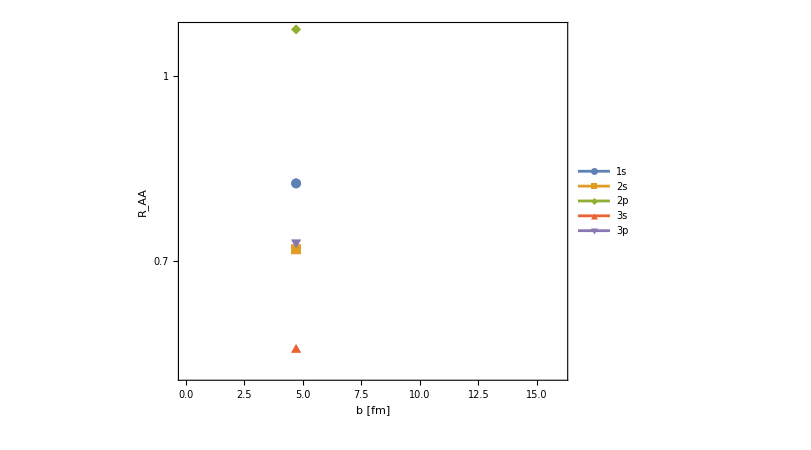

```mathematica
comp1=ListLogPlot[{raa1s,raa2s,raa2p,raa3s,raa3p},PlotRange->{{0,16},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->{Automatic,Medium},IntervalMarkers->"Bands",FrameLabel->{"b [fm]","R_AA"},PlotLegends->Placed[LineLegend[{Style["1s",16],Style["2s",16],Style["2p",16],Style["3s",16],Style["3p",16]},LegendMarkerSize->{{60,15}}],{0.2,0.8}]]
```

```mathematica
(*Export[wd<>"/figures/spvsnpart-"<>figureNameMap[dataDir]<>".pdf",npartPlot]*)
```

## Check distribution functions

```mathematica
metaData = rawData[[All,1]];
supData = rawData[[All,2]];
```

```mathematica
ptData = metaData[[All,5]];
yData = metaData[[All,7]];
```

```mathematica
𝒟=HistogramDistribution[yData,40];
testPlot=DiscretePlot[PDF[𝒟,x],{x,-10,10,.01}];
```

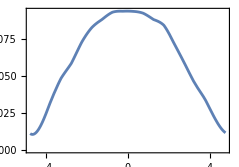
```mathematica
p1 = -Graphics-;
```

```mathematica
f[y_]:= 0.1(1- 2Sqrt[9.46^2+5^2]/5023 Cosh[y])^(13.8)
f2[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/5023 Cosh[y])^(13.8)
f3[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/8160 Cosh[y])^(13.8)
```

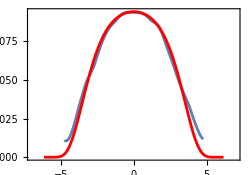

```mathematica
p2=Plot[{f[y](*,f2[y],f3[y]*)},{y,-7,7},PlotStyle->{Blue,Green,Red}];
Show[p1,p2,PlotRange->{{-7,7},All},ImageSize->250]
```

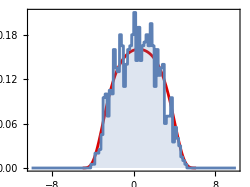

```mathematica
p3=Plot[1.7f[-y+0.5],{y,-5,6.1},PlotStyle->2];
Show[p3,testPlot,ImageSize->250]
```

## Results as a function of p_T averaged over centrality (with feed down)

### Setup

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] := 1splitHyperfine[x[[2]]]
```

```mathematica
selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax && #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&& #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
weightedList[ptmin_,ptmax_]:=Module[{wtm,temp},
wtm = Mean[selectWeights[ptmin,ptmax]];
selectPTweighted[ptmin,ptmax]/wtm
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_]:=Mean[weightedList[ptmin,ptmax]]
nAAsdevVsPT[ptmin_,ptmax_]:=StandardDeviation[weightedList[ptmin,ptmax]]/Sqrt[Length[selectPTweighted[ptmin,ptmax]]]
nAAVsPT[ptmin_,ptmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax];
err= nAAsdevVsPT[ptmin,ptmax];
Table[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

### -1.93 < y < 1.93

```mathematica
ymin = -1.93;
ymax = 1.93;
```

```mathematica
binwidth=2.5;
ptmax = 30;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

StandardDeviation::shlen: The argument {{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}} should have at least two elements.

Part::partw: Part 2 of StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}] does not exist.

Part::partw: Part 3 of StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}] does not exist.

Part::partw: Part 4 of StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StandardDeviation::shlen: The argument {{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}} should have at least two elements.

Part::partw: Part 2 of StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}] does not exist.

StandardDeviation::shlen: The argument {{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}} should have at least two elements.

Part::partw: Part 3 of StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}] does not exist.

StandardDeviation::shlen: The argument {{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

Part::partw: Part 4 of StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1.25,0.8050.004,0.6470.012,1.0480.010,1.0450.010,1.0460.010,0.5140.018,0.6320.019,0.6320.019,0.6320.019},{3.75,0.81030.0034,0.6570.009,1.0600.008,1.0570.008,1.0580.008,0.5230.014,0.6440.014,0.6440.014,0.6440.014},{6.25,0.8510.005,0.7390.012,1.1100.011,1.1070.010,1.1080.010,0.6220.020,0.7560.021,0.7560.021,0.7560.021},{8.75,0.8450.008,0.7190.017,1.0990.014,1.0960.014,1.0980.014,0.6020.028,0.7380.029,0.7380.029,0.7380.029},{11.25,0.8580.009,0.7500.021,1.1300.016,1.1270.016,1.1290.016,0.6340.035,0.780.04,0.780.04,0.780.04},{13.75,0.8440.015,0.7080.034,1.0790.028,1.0760.028,1.0780.028,0.600.06,0.740.06,0.740.06,0.740.06},{16.25,0.8430.016,0.700.04,1.0910.027,1.0880.027,1.0890.027,0.590.06,0.730.06,0.730.06,0.730.06},{18.75,0.8910.022,0.820.04,1.1610.035,1.1590.035,1.1600.035,0.720.08,0.870.08,0.870.08,0.870.08},{21.25,0.9280.022,0.870.05,1.150.04,1.150.04,1.150.04,0.810.08,0.950.08,0.950.08,0.950.08},{23.75,0.8650.026,0.740.06,1.100.05,1.100.05,1.100.05,0.640.09,0.790.09,0.790.09,0.790.09},{26.25,0.75010.0022,0.50130.0026,0.9670.010,0.9630.010,0.9650.010,0.3640.004,0.4870.014,0.4870.014,0.4870.014},{28.75,0.879852{{0.0173611 √(1284.01+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(1063.31+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(2751.05+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(2751.05+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(2751.05+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(795.481+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(1384.89+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(1384.89+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0173611 √(1384.89+15.3297 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2)}},0.773784{{0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2)}},1.21936{{0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦3⟧)^2)}},1.21653{{0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2)}},1.21777{{0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2)}},0.655689{{0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦6⟧)^2)}},0.865149{{0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦7⟧)^2)}},0.865149{{0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦8⟧)^2)}},0.865149{{0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.833042,0.758077,1.21936,1.21936,1.21936,0.655689,0.865149,0.865149,0.865149}}]⟦9⟧)^2)}}}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

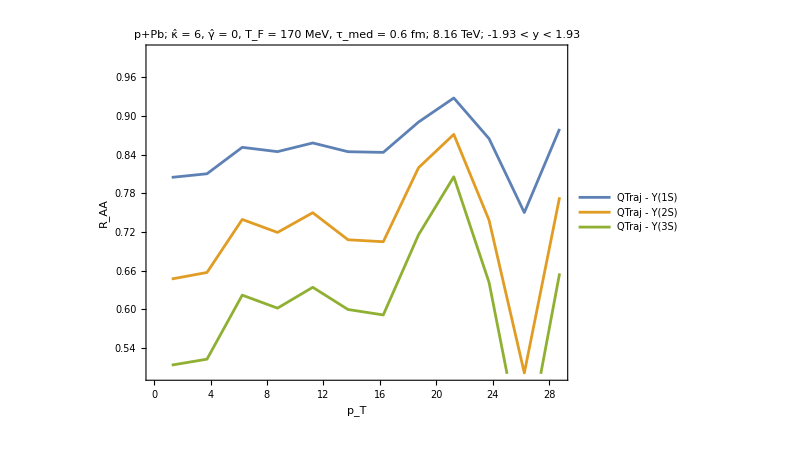

```mathematica
ptPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.5,1},PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax]]
```

```mathematica
fileName =dirName<>"/raavspt-central.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

### -5 < y < -2.5

```mathematica
ymin = -5;
ymax = -2.5;
```

```mathematica
binwidth=2.5;
ptmax = 23;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

StandardDeviation::shlen: The argument {{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}} should have at least two elements.

StandardDeviation::shlen: The argument {{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}} should have at least two elements.

StandardDeviation::shlen: The argument {} should have at least two elements.

Part::partw: Part 2 of StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}] does not exist.

Part::partw: Part 2 of StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}] does not exist.

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 3 of StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}] does not exist.

Part::partw: Part 3 of StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 4 of StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}] does not exist.

Part::partw: Part 4 of StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}] does not exist.

Part::partw: Part 2 of Mean[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

Join::heads: Heads List and Times at positions 1 and 2 are expected to be the same.

StandardDeviation::shlen: The argument {{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}} should have at least two elements.

Part::partw: Part 2 of StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}] does not exist.

StandardDeviation::shlen: The argument {{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}} should have at least two elements.

Part::partw: Part 3 of StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}] does not exist.

StandardDeviation::shlen: The argument {{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

Part::partw: Part 4 of StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

Join::heads: Heads List and Times at positions 1 and 2 are expected to be the same.

Dot::rect: Nonrectangular tensor encountered.

Join::heads: Heads List and Times at positions 1 and 2 are expected to be the same.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Join::heads: Heads List and Times at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

{{1.25,0.8890.012,0.8310.027,1.1810.015,1.1780.015,1.1790.015,0.730.05,0.880.05,0.880.05,0.880.05},{3.75,0.8920.009,0.8290.019,1.1730.014,1.1700.014,1.1720.014,0.7260.034,0.8750.033,0.8750.033,0.8750.033},{6.25,0.8960.016,0.8240.033,1.1430.023,1.1410.023,1.1420.023,0.730.06,0.870.06,0.870.06,0.870.06},{8.75,0.8660.007,0.7640.020,1.1910.018,1.1880.018,1.1890.018,0.6410.033,0.820.04,0.820.04,0.820.04},{11.25,0.825018{{0.0173611 √(1172.66+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(802.417+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(2359.8+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(2359.8+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(2359.8+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(506.932+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(892.55+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(892.55+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0173611 √(892.55+15.3297 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2)}},0.660003{{0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2)}},1.12933{{0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦3⟧)^2)}},1.12586{{0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2)}},1.12738{{0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2)}},0.523429{{0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦6⟧)^2)}},0.694543{{0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦7⟧)^2)}},0.694543{{0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦8⟧)^2)}},0.694543{{0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.796102,0.658541,1.12933,1.12933,1.12933,0.523429,0.694543,0.694543,0.694543}}]⟦9⟧)^2)}}},{13.75,0.820321{{0.0173611 √(1165.73+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(760.211+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(2324.95+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(2324.95+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(2324.95+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(478.326+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(862.864+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(862.864+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0173611 √(862.864+15.3297 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2)}},0.643628{{0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2)}},1.12096{{0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦3⟧)^2)}},1.11747{{0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2)}},1.119{{0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2)}},0.508446{{0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦6⟧)^2)}},0.682895{{0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦7⟧)^2)}},0.682895{{0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦8⟧)^2)}},0.682895{{0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.793745,0.640988,1.12096,1.12096,1.12096,0.508446,0.682895,0.682895,0.682895}}]⟦9⟧)^2)}}},Join[{16.25},{{1.,0.2645,0.0194,0.352,0.18,0.0657,0.0038,0.1153,0.077},{0.,1.,0.,0.,0.,0.106,0.0138,0.181,0.089},{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.0091,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.0051},{0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.}}.{{},14.8027 Mean[{}]⟦2⟧14.8027 ComplexInfinity⟦2⟧,3.72 Mean[{}]⟦3⟧3.72 ComplexInfinity⟦3⟧,13.5808 Mean[{}]⟦4⟧13.5808 ComplexInfinity⟦4⟧,16.0278 Mean[{}]⟦5⟧16.0278 ComplexInfinity⟦5⟧,6.8 Mean[{}]⟦6⟧6.8 ComplexInfinity⟦6⟧,3.27 Mean[{}]⟦7⟧3.27 ComplexInfinity⟦7⟧,12. Mean[{}]⟦8⟧12. ComplexInfinity⟦8⟧,14.15 Mean[{}]⟦9⟧14.15 ComplexInfinity⟦9⟧} {0.0173611,0.0526316,0.268817,0.073046,0.0621118,0.147059,0.30581,0.0833333,0.0706714}],Join[{18.75},{{1.,0.2645,0.0194,0.352,0.18,0.0657,0.0038,0.1153,0.077},{0.,1.,0.,0.,0.,0.106,0.0138,0.181,0.089},{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.0091,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.0051},{0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.}}.{{},14.8027 Mean[{}]⟦2⟧14.8027 ComplexInfinity⟦2⟧,3.72 Mean[{}]⟦3⟧3.72 ComplexInfinity⟦3⟧,13.5808 Mean[{}]⟦4⟧13.5808 ComplexInfinity⟦4⟧,16.0278 Mean[{}]⟦5⟧16.0278 ComplexInfinity⟦5⟧,6.8 Mean[{}]⟦6⟧6.8 ComplexInfinity⟦6⟧,3.27 Mean[{}]⟦7⟧3.27 ComplexInfinity⟦7⟧,12. Mean[{}]⟦8⟧12. ComplexInfinity⟦8⟧,14.15 Mean[{}]⟦9⟧14.15 ComplexInfinity⟦9⟧} {0.0173611,0.0526316,0.268817,0.073046,0.0621118,0.147059,0.30581,0.0833333,0.0706714}],Join[{21.25},{{1.,0.2645,0.0194,0.352,0.18,0.0657,0.0038,0.1153,0.077},{0.,1.,0.,0.,0.,0.106,0.0138,0.181,0.089},{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.0091,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.0051},{0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.}}.{{},14.8027 Mean[{}]⟦2⟧14.8027 ComplexInfinity⟦2⟧,3.72 Mean[{}]⟦3⟧3.72 ComplexInfinity⟦3⟧,13.5808 Mean[{}]⟦4⟧13.5808 ComplexInfinity⟦4⟧,16.0278 Mean[{}]⟦5⟧16.0278 ComplexInfinity⟦5⟧,6.8 Mean[{}]⟦6⟧6.8 ComplexInfinity⟦6⟧,3.27 Mean[{}]⟦7⟧3.27 ComplexInfinity⟦7⟧,12. Mean[{}]⟦8⟧12. ComplexInfinity⟦8⟧,14.15 Mean[{}]⟦9⟧14.15 ComplexInfinity⟦9⟧} {0.0173611,0.0526316,0.268817,0.073046,0.0621118,0.147059,0.30581,0.0833333,0.0706714}]}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

Join::heads: Heads List and Times at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::partw: Part {1,3} of … does not exist.

Part::partw: Part {1,7} of … does not exist.

```mathematica
ptPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.5,1},PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax]]
```

ListPlot::lpn: {«1»} is not a list of numbers or pairs of numbers.

```mathematica
fileName =dirName<>"/raavspt-backward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

### 1.5 < y < 4

```mathematica
ymin = 1.5;
ymax = 4;
```

```mathematica
binwidth=2.5;
ptmax = 23;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

{{1.25,0.8160.007,0.6740.017,1.0730.015,1.0690.015,1.0710.015,0.5400.027,0.6630.028,0.6630.028,0.6630.028},{3.75,0.8230.005,0.6810.013,1.0710.011,1.0680.010,1.0690.011,0.5540.020,0.6790.020,0.6790.020,0.6790.020},{6.25,0.8440.007,0.7270.018,1.1120.015,1.1090.015,1.1110.015,0.6040.029,0.7410.030,0.7410.030,0.7410.030},{8.75,0.8540.012,0.7340.027,1.1220.022,1.1200.022,1.1210.022,0.620.05,0.770.05,0.770.05,0.770.05},{11.25,0.8970.017,0.8110.033,1.1440.028,1.1420.027,1.1430.028,0.720.06,0.870.05,0.870.05,0.870.05},{13.75,0.8270.014,0.680.04,1.120.05,1.110.05,1.120.05,0.550.07,0.700.08,0.700.08,0.700.08},{16.25,0.8430.029,0.700.06,1.0390.032,1.0370.032,1.0380.032,0.590.09,0.700.08,0.700.08,0.700.08},{18.75,0.75790.0032,0.540.04,0.98340.0034,0.97950.0034,0.98120.0034,0.3880.018,0.4960.007,0.4960.007,0.4960.007},{21.25,0.920.05,0.860.10,1.1900.004,1.1880.005,1.1890.004,0.780.18,0.960.17,0.960.17,0.960.17}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

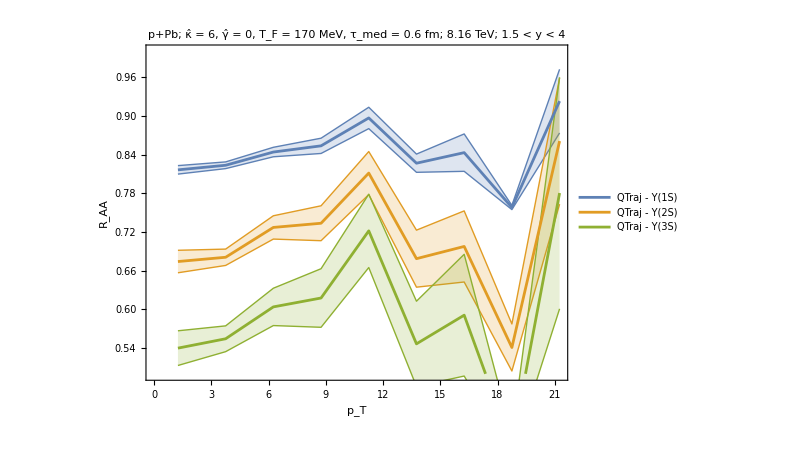

```mathematica
ptPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.5,1},PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax]]
```

```mathematica
fileName =dirName<>"/raavspt-forward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

## Results as a function of y averaged over centrality and p_T (with feed down)

#### Setup

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] :=  1*splitHyperfine[ x[[2]][[1;;6]] ]
```

```mathematica
selectWeights[ymin_,ymax_]:=getWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
selectYweighted[ymin_,ymax_]:=mapWithWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
weightedList[ymin_,ymax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ymin,ymax]];
res = selectYweighted[ymin,ymax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsY[ymin_,ymax_]:= Module[{wl,num,qweights},
wl=weightedList[ymin,ymax];
qweights = ConstantArray[1,Length[wl]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsY[ymin_,ymax_]:=Module[{wl},
wl = weightedList[ymin,ymax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsY[ymin_,ymax_]:=Module[{avg,err},
avg = nAAavgVsY[ymin,ymax];
err= nAAsdevVsY[ymin,ymax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Results

```mathematica
binwidth=0.5;
ymax =5;
(* flip y here due to inverse in hydro setup *)
naavsyData=Reverse[Table[Join[{-x+-binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

StandardDeviation::shlen: The argument {} should have at least two elements.

Power::infy: Infinite expression 1/0 encountered.

Part::partd: Part specification Indeterminate⟦1⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦2⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦3⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦4⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦5⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦6⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦7⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦8⟧ is longer than depth of object.

Part::partd: Part specification Indeterminate⟦9⟧ is longer than depth of object.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

Part::partw: Part 3 of ComplexInfinity does not exist.

Part::partw: Part 4 of ComplexInfinity does not exist.

Part::partw: Part 5 of ComplexInfinity does not exist.

Part::partw: Part 6 of ComplexInfinity does not exist.

Part::partw: Part 7 of ComplexInfinity does not exist.

Part::partw: Part 8 of ComplexInfinity does not exist.

Part::partw: Part 9 of ComplexInfinity does not exist.

Part::partd: Part specification Indeterminate⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partd: Part specification Indeterminate⟦2⟧ is longer than depth of object.

Part::partw: Part 2 of ComplexInfinity does not exist.

Part::partd: Part specification Indeterminate⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StandardDeviation::shlen: The argument {{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}} should have at least two elements.

Part::partw: Part 2 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 3 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 4 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 5 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 6 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 7 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 8 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

Part::partw: Part 9 of StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}] does not exist.

StandardDeviation::shlen: The argument {{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{{-4.75,0.9700.010,0.9790.009,1.2090.023,1.2080.023,1.2080.023,0.9330.019,1.0900.017,1.0900.017,1.0900.017},{-4.25,0.9310.010,0.9050.014,1.2070.014,1.2060.014,1.2060.014,0.8250.028,0.9860.024,0.9860.024,0.9860.024},{-3.75,0.8930.009,0.8280.017,1.1650.012,1.1630.012,1.1640.012,0.7260.031,0.8710.029,0.8710.029,0.8710.029},{-3.25,0.8430.008,0.7270.020,1.1270.016,1.1240.016,1.1250.016,0.6000.033,0.7420.035,0.7420.035,0.7420.035},{-2.75,0.8310.006,0.6950.015,1.0910.012,1.0880.012,1.0890.012,0.5680.025,0.7010.025,0.7010.025,0.7010.025},{-2.25,0.8190.008,0.6660.017,1.0550.014,1.0520.014,1.0530.014,0.5400.028,0.6610.028,0.6610.028,0.6610.028},{-1.75,0.8150.006,0.6630.015,1.0590.013,1.0560.013,1.0570.013,0.5330.023,0.6580.024,0.6580.024,0.6580.024},{-1.25,0.8130.006,0.6600.015,1.0570.013,1.0530.013,1.0550.013,0.5310.023,0.6550.024,0.6550.024,0.6550.024},{-0.75,0.8180.007,0.6650.017,1.0490.014,1.0460.014,1.0470.014,0.5420.027,0.6640.028,0.6640.028,0.6640.028},{-0.25,0.8150.005,0.6640.013,1.0660.011,1.0630.011,1.0650.011,0.5310.021,0.6570.022,0.6570.022,0.6570.022},{0.25,0.8300.006,0.6950.014,1.0850.012,1.0820.012,1.0830.012,0.5690.023,0.6980.024,0.6980.024,0.6980.024},{0.75,0.8500.008,0.7320.018,1.0890.013,1.0860.013,1.0870.013,0.6200.030,0.7450.030,0.7450.030,0.7450.030},{1.25,0.8420.006,0.7210.014,1.1150.012,1.1120.012,1.1140.012,0.5970.023,0.7380.024,0.7380.024,0.7380.024},{1.75,0.8480.006,0.7370.014,1.1240.011,1.1210.011,1.1230.011,0.6130.023,0.7520.023,0.7520.023,0.7520.023},{2.25,0.8500.008,0.7330.018,1.1110.011,1.1080.011,1.1090.011,0.6110.030,0.7440.028,0.7440.028,0.7440.028},{2.75,0.8800.008,0.7970.016,1.1490.011,1.1470.011,1.1480.011,0.6910.028,0.8350.027,0.8350.027,0.8350.027},{3.25,0.8840.008,0.8150.020,1.2000.011,1.1970.011,1.1980.011,0.700.04,0.870.04,0.870.04,0.870.04},{3.75,0.9270.011,0.9060.025,1.2370.007,1.2360.007,1.2360.007,0.820.05,1.000.05,1.000.05,1.000.05},{4.25,0.928349{{0.0173611 √(1392.18+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(1486.34+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(2942.52+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(2942.52+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(2942.52+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(1264.84+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(1908.97+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(1908.97+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(1908.97+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0173611 √(1908.97+15.3297 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.00520822 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2+22.8526 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+8.32328 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.199594 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.000154405 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+1.91435 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.18712 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2)}},0.915498{{0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0526316 √(0.+219.121 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦2⟧)^2+0.519553 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2+0.00203636 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2+4.71758 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2+1.58596 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2)}},1.26108{{0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2),0.268817 √(0.+13.8384 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦3⟧)^2)}},1.25912{{0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.073046 √(0.+184.438 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦4⟧)^2+0.0119246 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2)}},1.25998{{0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0621118 √(0.+256.891 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦5⟧)^2+0.00520779 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2)}},0.826799{{0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2),0.147059 √(0.+46.24 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦6⟧)^2)}},1.01574{{0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2),0.30581 √(0.+10.6929 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦7⟧)^2)}},1.01574{{0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2),0.0833333 √(0.+144. (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦8⟧)^2)}},1.01574{{0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2),0.0706714 √(0.+200.223 (StandardDeviation[{{0.867421,0.896275,1.26108,1.26108,1.26108,0.826799,1.01574,1.01574,1.01574,1.01574}}]⟦9⟧)^2)}}},{4.75,0.0173611 (43.0147 Indeterminate⟦1⟧+3.91532 Indeterminate⟦2⟧+0.072168 Indeterminate⟦3⟧+4.78044 Indeterminate⟦4⟧+2.88501 Indeterminate⟦5⟧+0.44676 Indeterminate⟦6⟧+0.012426 Indeterminate⟦7⟧+1.3836 Indeterminate⟦8⟧+1.08955 Indeterminate⟦9⟧)0.0173611 √(1850.27 ComplexInfinity⟦1⟧^2+15.3297 ComplexInfinity⟦2⟧^2+0.00520822 ComplexInfinity⟦3⟧^2+22.8526 ComplexInfinity⟦4⟧^2+8.32328 ComplexInfinity⟦5⟧^2+0.199594 ComplexInfinity⟦6⟧^2+0.000154405 ComplexInfinity⟦7⟧^2+1.91435 ComplexInfinity⟦8⟧^2+1.18712 ComplexInfinity⟦9⟧^2),0.0526316 (0.+14.8027 Indeterminate⟦2⟧+0.7208 Indeterminate⟦6⟧+0.045126 Indeterminate⟦7⟧+2.172 Indeterminate⟦8⟧+1.25935 Indeterminate⟦9⟧)0.0526316 √(219.121 ComplexInfinity⟦2⟧^2+0.519553 ComplexInfinity⟦6⟧^2+0.00203636 ComplexInfinity⟦7⟧^2+4.71758 ComplexInfinity⟦8⟧^2+1.58596 ComplexInfinity⟦9⟧^2),0.268817 (0.+3.72 Indeterminate⟦3⟧)1. ComplexInfinity⟦3⟧,0.073046 (0.+13.5808 Indeterminate⟦4⟧+0.1092 Indeterminate⟦8⟧)0.073046 √(184.438 ComplexInfinity⟦4⟧^2+0.0119246 ComplexInfinity⟦8⟧^2),0.0621118 (0.+16.0278 Indeterminate⟦5⟧+0.072165 Indeterminate⟦9⟧)0.0621118 √(256.891 ComplexInfinity⟦5⟧^2+0.00520779 ComplexInfinity⟦9⟧^2),0.147059 (0.+6.8 Indeterminate⟦6⟧)1. ComplexInfinity⟦6⟧,0.30581 (0.+3.27 Indeterminate⟦7⟧)1. ComplexInfinity⟦7⟧,0.0833333 (0.+12. Indeterminate⟦8⟧)1. ComplexInfinity⟦8⟧,0.0706714 (0.+14.15 Indeterminate⟦9⟧)1. ComplexInfinity⟦9⟧}}

```mathematica
naa1s =naavsyData[[All,{1,2}]] ;
naa2s = naavsyData[[All,{1,3}]] ;
naa3s = naavsyData[[All,{1,7}]] ;
```

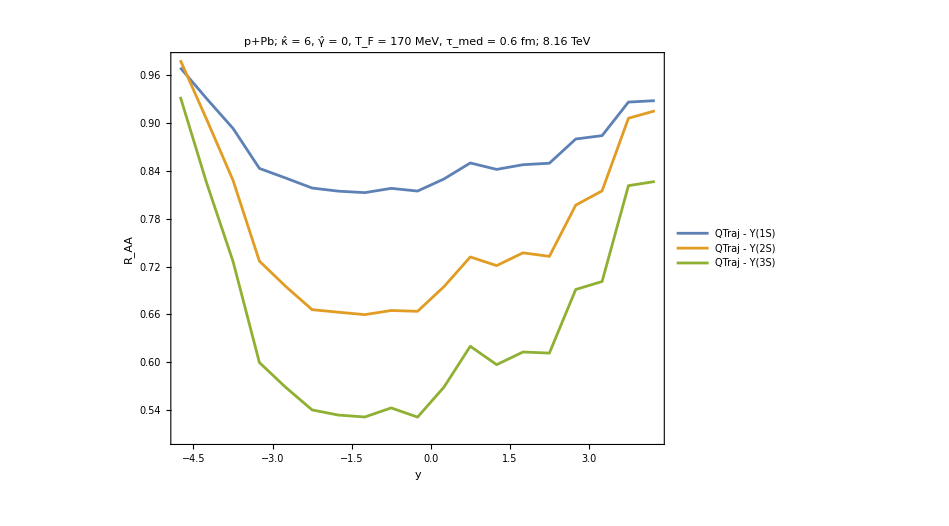

```mathematica
yPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"y","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->All,PlotLabel->labelMap[dataDir]]
```

```mathematica
fileName =dirName<>"/rpavsy.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvsy={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvsy]
```

#### Results - integrate

```mathematica
binwidth=10;
ymax =5;
(* flip y here due to inverse in hydro setup *)
naavsyData=Reverse[Table[Join[{-x+-binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N]
```

{{0.,0.83880.0018,0.7130.004,1.0950.004,1.09200.0035,1.09330.0035,0.5910.007,0.7230.007,0.7230.007,0.7230.007}}

```mathematica
naa1s =naavsyData[[All,{1,2}]] ;
naa2s = naavsyData[[All,{1,3}]] ;
naa3s = naavsyData[[All,{1,7}]] ;
```

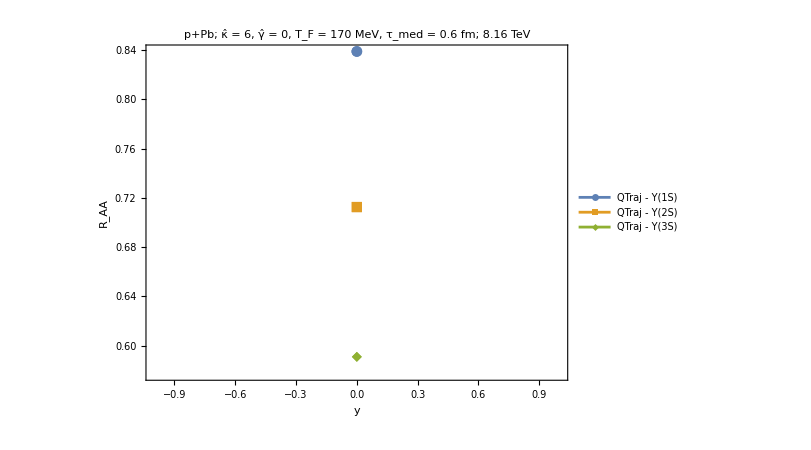

```mathematica
yPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,IntervalMarkers->"Bands",FrameLabel->{"y","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,20}}],{Right,Bottom}],PlotLabel->labelMap[dataDir],PlotMarkers->Automatic]
```

```mathematica
fileName =dirName<>"/raavsy.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvsy={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvsy]
```